## Growth-rate driven modelling study

#### Supplementary material to Hamis, Browning, Jenner, Villa, Maini, Cassidy (2025).

In this Notebook we calculate
𝜆_eff = 1/τ (∫_0^t_on FM(x(t),d)ⅆt + ∫_t_on^t_off FM(x(t),0)ⅆt )
for different choices of 𝑡_on (the duration that the drug is on) and 𝑡_off (the duration that the drug is off).

#### Define growth rates as functions of the phenotype state x:

In the notebook, FMxd denotes FM(x,d) where 
x=0 is the least drug-adapted phenotype state, 
x=1 is the most drug adapted phenotype state,
d=0 means “drug is off”, 
d=D means “drug is on” at a selected dose D.

```mathematica
λ0[x_]:=FM00+(FM10-FM00)x (* no drug *)
λ1[x_]:=FM0D+(FM1D-FM0D)x (* drug *)
```

#### State assumptions:

```mathematica
$Assumptions=ω>0;
```

#### Case 1: t_on,t_off>1/ω .

Drug on: Phenotypes start at x=0, reach x=1 during climbing period of length 1/ω,  and then stay at x=1 until time t_on. 
Drug off: Cells reach x=0 during a descending period of length 1/ω, and then stay at x=0 until time t_on+ t_off. 
A plot is shown below for (arbitrarily selected) values of t_on,t_off, ω such that Case 1 holds.

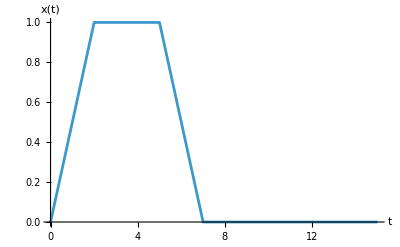

```mathematica
x[t_]:=Piecewise[{{ω t,t<1/ω},{1,1/ω<=t<=ton},{1-ω (t-ton),ton<t<ton+1/ω},{0,t>=ton+1/ω}}];
Plot[x[t]/.{ω->0.5,ton->5,toff->10},{t,0,15},AxesLabel->{"t","x(t)"}]
```

We now symbolically calculate and simplify the expression for the Case 1 integral using
ΔFM(𝑑) = FM(1, 𝑑) − FM(0, 𝑑).

```mathematica
C1=1/τ FullSimplify[
  Integrate[λ1[ω t],{t,0,1/ω}]+
Integrate[λ1[1],{t,1/ω,ton}]+
Integrate[λ0[1-ω (t-ton)],{t,ton,ton+1/ω}]+
Integrate[λ0[0],{t,ton+1/ω,ton+toff}]
]/.{FM10-FM00-> ΔFM0}/.{FM0D-FM1D-> -ΔFMD}
```

(FM00 toff+FM1D ton+(ΔFM0-ΔFMD)/(2 ω))/τ

Now customised, numerical values for  t_on, t_off, ω, can be inserted into the expression for C1 to obtain 𝜆_eff .

```mathematica
C1num=C1/.{ΔFM0->FM10-FM00,ΔFMD->FM1D-FM0D, τ->ton+toff}; (*Writing C1 in long format*)
C1num/.{FM0D->-0.2866,FM1D->0.0741,FM00->0.1374,FM10->0.07067,
ω->0.5,ton ->5,toff->10} (*As used in the above plot*)
```

0.0878047

#### Case 2: t_on<t_off<1/ω .

Drug on: Phenotypes start at x=0, and then reach x=ωt during climbing period of length t_on. 
Drug off: Cells reach x=0 during a descending period of length t_on, and then stay at x=0 until time t_on+ t_off. 
A plot is shown below for (arbitrarily selected) values of t_on,t_off, ω such that Case 2 holds.

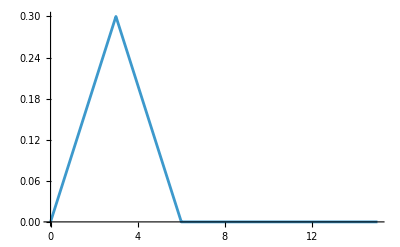

```mathematica
x[t_]:=Piecewise[{{ω t,t<ton},{ω ton - ω (t - ton),ton<=t<2ton},{0,2 ton<=t<=ton+toff}}]
Plot[x[t]/.{ω->0.1,ton->3,toff->10},{t,0,15}]
```

We now symbolically calculate and simplify the expression for the Case 2 integral using
ΔFM(𝑑) = FM(1, 𝑑) − FM(0, 𝑑).

```mathematica
C2=1/τ FullSimplify[
  Integrate[λ1[ω t],{t,0,ton}]+
Integrate[λ0[ω ton - ω (t - ton)],{t,ton,2ton}]+
Integrate[λ0[0],{t,2ton,ton+toff}]
]/.{FM10-FM00->ΔFM0}/.{-FM0D+FM1D->ΔFM1}
```

(FM00 toff+FM0D ton+1/2 ton^2 (ΔFM0+ΔFM1) ω)/τ

#### Case 3: t_off<t_on<1/ω .

Drug off: Phenotypes start at x=1, and then reach x=ωt during descending period of length t_off. 
Drug on: Phenotypes reach x=1 during climbing period of length t_off, and then stay at x=1 until time t_on+ t_off.
A plot is shown below for (arbitrarily selected) values of t_on,t_off, ω such that Case 2 holds.

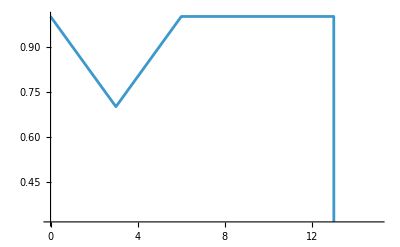

```mathematica
x[t_]:=Piecewise[{{1-ω t ,t<toff},{1-ω toff + ω (t-toff),toff<=t<2 toff},{1,2 toff<=t<=ton+toff}}]
Plot[x[t]/.{ω->0.1,ton->10,toff->3},{t,0,15}]
```

```mathematica
C3=1/T FullSimplify[
  Integrate[λ0[1-ω t],{t,0,toff}]+ 
Integrate[λ1[1-ω toff + ω (t-toff)],{t,toff,2 toff}]+ 
Integrate[λ1[1],{t,2 toff,ton+toff}] 
]/.{FM0D-FM1D->-ΔFMD}  /.{FM00-FM10->-ΔFM0}
```

(FM10 toff+FM1D ton+1/2 toff^2 (-ΔFM0-ΔFMD) ω)/T

#### Case 4: t_on=t_off = T/2=1/ω .

Drug on: Phenotypes start at x=0, and then reach x=1 during climbing period of length T/2. 
Drug off: Cells reach x=0 during a descending period of length T/2. 
A plot is shown below for (arbitrarily selected) values of t_on=t_off such that Case 2 holds.

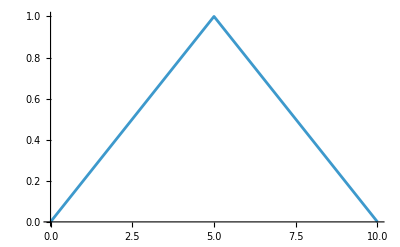

```mathematica
x[t_]:=Piecewise[{{ω t ,t<ton},{1- ω (t-ton),ton<=t<2 ton}}]
Plot[x[t]/.{ω->1/5,ton->5},{t,0,10}]
```

We now symbolically calculate and simplify the expression for the Case 4 integral.

```mathematica
C4=1/(2*ton)FullSimplify[
  Integrate[λ1[ω t],{t,0,ton}]+
Integrate[λ0[1-ω (t-(ton))],{t,ton,2*ton}]
]/.{ton*ω -> 1} /.{-FM0D-FM10+2 (FM0D+FM10)->FM0D+FM10 }
```

1/4 (FM00+FM0D+FM10+FM1D)

#### We now consider Case 5 and 6 where t_on=t_off= T. Case 5: T<1/ω. Case 6: T>1/ω,

```mathematica
C5=1/(2T)FullSimplify[
  Integrate[λ1[ω t],{t,0,T}]+
Integrate[λ0[ω T-ω (t-T)],{t,T,2 T}]
]/.{-FM0D+FM1D->ΔFMD}/.{-FM00+FM10->ΔFM0}
```

1/4 (2 (FM00+FM0D)+T (ΔFM0+ΔFMD) ω)

```mathematica
C6=1/(2T)FullSimplify[
  Integrate[λ1[ω t],{t,0,1/ω}]+
Integrate[λ1[1],{t,1/ω,T}]+
Integrate[λ0[1-ω (t-T)],{t,T,T+1/ω}]+
Integrate[λ0[0],{t,T+1/ω,2T}]
]/.{FM0D-FM1D->-ΔFMD}/.{-FM00+FM10->ΔFM0}
```

((FM00+FM1D) T+(ΔFM0-ΔFMD)/(2 ω))/(2 T)